```mathematica
Limit[Assuming[{p∈Reals,a∈Reals,a>0},Integrate[r Sinc[p r]Exp[-a r],{r,0,∞}]],a->0]
```

1/p^2

```mathematica
Assuming[{p∈Reals,a∈Reals,a>0},Integrate[r^5 Sinc[p r]Exp[-a r],{r,0,∞}]]
```

(24 (5 a^4-10 a^2 p^2+p^4))/((a^2+p^2)^5)

```mathematica
Assuming[{p∈Reals,a∈Reals,a>0},Integrate[Sinc[p r](2 (-3 a^2+p^2))/((a^2+p^2)^3),{p,0,∞}]]
```

ConditionalExpression[(ⅇ^(-a Abs[r]) π (6-6 ⅇ^(a Abs[r])+a^2 r^2+4 a Abs[r]))/(2 a^4 Abs[r]),r∈Reals]

```mathematica
Assuming[{p∈Reals,a∈Reals,a>0},Integrate[Sinc[p r] p^2(-b a^2+p^2)/((a^2+p^2)^3),{p,0,∞}]]
```

ConditionalExpression[-(ⅇ^(-a Abs[r]) π (-3+b+a (1+b) Abs[r]))/(16 a),r∈Reals]

```mathematica
Assuming[{r∈Reals,a∈Reals,a>0,b∈Reals,mD∈Reals},Integrate[(-b a^2+p^2)/((a^2+p^2)^4(p^2+mD^2)) p^4 Sinc[p r],{p,0,∞}]]
```

Resultant::ivar: 1 is not a valid variable.

$Aborted

```mathematica
Limit[Assuming[{mD∈Reals,a∈Reals,a>0,r∈Reals,r>0},Integrate[1/(p^2+mD^2)Sinc[p r]Exp[-a p],{p,0,∞}]],a->0]
```

$Aborted

```mathematica
Limit[Assuming[{mD∈Reals,a∈Reals,a>0,n∈Reals,n>0},Integrate[p^2/(p^2+mD^2)Sinc[p r]Exp[-a p],{p,0,∞}]],a->0]
```

ConditionalExpression[1/(8 r)ⅇ^(-mD r) (π-ⅇ^(2 mD r) π+2 ⅈ ((1+ⅇ^(2 mD r)) CosIntegral[-ⅈ mD r]-(1+ⅇ^(2 mD r)) CosIntegral[ⅈ mD r]+Log[-ⅈ/mD]-ⅇ^(2 mD r) Log[-ⅈ/mD]+Log[mD]-ⅇ^(2 mD r) Log[mD]+Log[-ⅈ r]+ⅇ^(2 mD r) Log[-ⅈ r]-Log[ⅈ r]-ⅇ^(2 mD r) Log[ⅈ r]-Log[-ⅈ mD r]-ⅇ^(2 mD r) Log[-ⅈ mD r]+Log[ⅈ mD r]+ⅇ^(2 mD r) Log[ⅈ mD r])),mD≠0&&Abs[Im[r]]<1]

```mathematica
Limit[Assuming[{mD∈Reals,a∈Reals,a>0,n∈Reals,n>0},Integrate[p^4/(p^2+mD^2)Sinc[p r]Exp[-a p],{p,0,∞}]],a->0]
```

ConditionalExpression[1/(8 r)ⅇ^(-mD r) mD^2 ((-1+ⅇ^(2 mD r)) π-2 ⅈ ((1+ⅇ^(2 mD r)) CosIntegral[-ⅈ mD r]-(1+ⅇ^(2 mD r)) CosIntegral[ⅈ mD r]+Log[-ⅈ/mD]-ⅇ^(2 mD r) Log[-ⅈ/mD]+Log[mD]-ⅇ^(2 mD r) Log[mD]+Log[-ⅈ r]+ⅇ^(2 mD r) Log[-ⅈ r]-Log[ⅈ r]-ⅇ^(2 mD r) Log[ⅈ r]-Log[-ⅈ mD r]-ⅇ^(2 mD r) Log[-ⅈ mD r]+Log[ⅈ mD r]+ⅇ^(2 mD r) Log[ⅈ mD r])),mD≠0&&Abs[Im[r]]<1]

```mathematica
Limit[Assuming[{mD∈Reals,a∈Reals,a>0,n∈Reals,n>0},Integrate[p^n/(p^2+mD^2)Sinc[p r]Exp[-a p],{p,0,∞}]],a->0]
```

Resultant::ivar: 1 is not a valid variable.

$Aborted

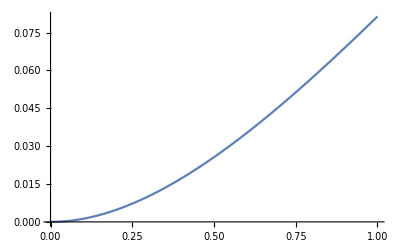

```mathematica
Plot[(π (-2+Abs[x]+(2+Abs[x]) Cosh[x]-(2+Abs[x]) Sinh[Abs[x]]))/(4 Abs[x]),{x,0,1}]
```

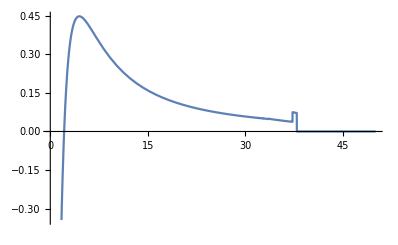

```mathematica
Plot[(π (-2+Abs[x]+(2+Abs[x]) Cosh[x]-(2+Abs[x]) Sinh[Abs[x]]))/(4 Abs[x])/(x^2/9)(-4+3 EulerGamma+3 Log[x]),{x,0,50}]
```

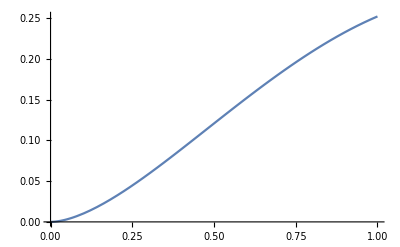

```mathematica
Plot[-x^2/9(-4+3 EulerGamma+3 Log[x]),{x,0,1}]
```

```mathematica
ImVs[a1_,mD_,σ_]:=Block[{a=a1,temp= π 0.155 0.2^2 σ^2 Quiet[NIntegrate[1/(p^3 (p^2+mD^2)^2) Sinc[0],{p,a,∞}]]},Interpolation[ParallelTable[{r,π 0.155 0.2^2 σ^2 Quiet[NIntegrate[1/(p^3 (p^2+mD^2)^2) Sinc[p r],{p,a,∞}]]-temp},{r,0,50,1/10}]]];
```

```mathematica
ReVsm0[a1_,mD_,σ_]:=Block[{a=a1,temp=1/(2 π^2)Quiet[NIntegrate[1/p^4 Sinc[0],{p,a,∞}]]},Interpolation[ParallelTable[{r,1/(2 π^2) Quiet[NIntegrate[1/p^4 Sinc[p r],{p,a,∞}]]-temp},{r,0,50,1/10}]]];
```

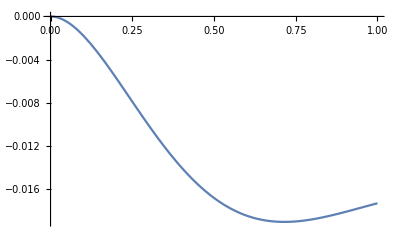

```mathematica
ReVsInter=Quiet[ReVsm0[1,0.2,0.17]];
Plot[ReVsInter[x/0.197],{x,0,1},PlotRange->All]
```

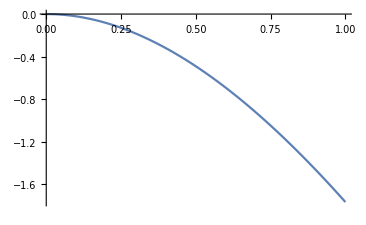

```mathematica
ReVsInter=Quiet[ReVsm0[1/10,0.2,0.17]];
Plot[ReVsInter[x/0.197],{x,0,1},PlotRange->All]
```

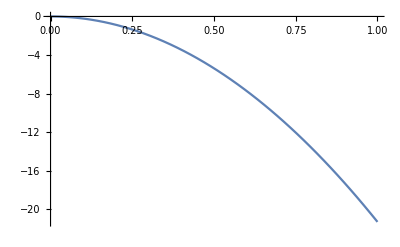

```mathematica
ReVsInter=Quiet[ReVsm0[1/100,0.2,0.17]];
Plot[ReVsInter[x/0.197],{x,0,1},PlotRange->All]
```

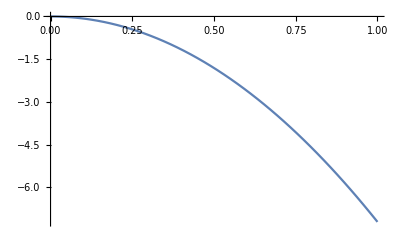

```mathematica
ReVsInter=Quiet[ImVs[1/1000,0.2,0.17]];
Plot[ReVsInter[x/0.197],{x,0,1},PlotRange->All]
```

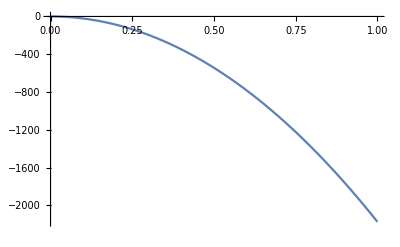

```mathematica
ReVsInter=Quiet[ReVsm0[1/10000,0.2,0.17]];
Plot[ReVsInter[x/0.197],{x,0,1},PlotRange->All]
```

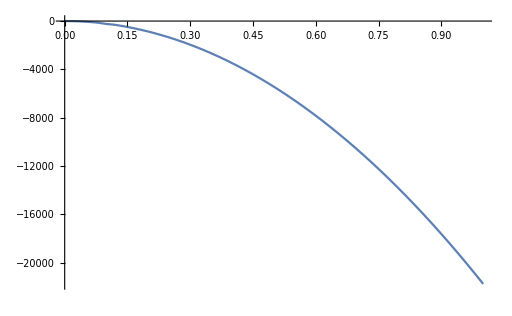

```mathematica
ReVsInter=Quiet[ReVsm0[1/100000,0.2,0.17]];
Plot[ReVsInter[x/0.197],{x,0,1},PlotRange->All]
```